{{124,643},{124.6,508},{125.3,479},{126.15,441}}

FittedModel[7691.29-57.0189 x]

7691.29-57.0189 x

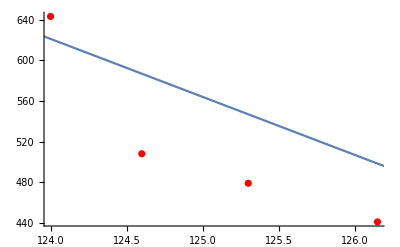

```mathematica
data={{123.5,667},{124.3,587},{125.86,492},{126.35,504},{127.1,447},{127.25,438}};
data1={{124,643},{124.6,508},{125.3,479},{126.15,441}}
model=LinearModelFit[data,x,x]
model["BestFit"]
p1=ListPlot[data1,PlotStyle->Red];
p2= Plot[model["BestFit"],{x,0,135}];
Show[p1,p2]
```

```mathematica
7772.620807118686-57.75838125567562 x
```

7772.62-57.7584 x

```mathematica
f[x_]:=7691.2923375208575-57.01886900833175 x
f[126.55]
```

475.554

```mathematica
f[127.2]
```

438.492

550.819

486.958

435.641